# Image Classification with Neural Networks

## Introduction

As a part of this project, I will explore image classification in Mathematica featuring the finest of machine learning techniques - neural networks. In order to perform image classification using neural networks successfully, several steps need to be taken including data preprocessing (transformation of data (images)), setting up layers for neural networks, determining training rounds (epochs) etc.  So, let’s just start with understanding neural networks first and how it is going to be the master mind here in this problem of image classification.

Problem Statement: Classify the characters of the well-known entertainment series - F.R.I.E.N.D.S. Use the classification model to classify: 
(1) Unknown images of characters of the series - classifier must recognize the image correctly.
(2) Unknown images of random characters - classifier should classify the image to the nearest possible match (w.r.t. the series characters) studying facial features.

-Graphics-

## Major Terminologies

A neural network can be perceived as a loosely modelled human brain, which is capable to recognize patterns by interpreting sensory data through a kind of machine perception or labelling raw input data. Just like the human brain, the individual units of neural networks are termed as neurons which are located in a series of groups called as layers.  Neurons in each layer are connected to neurons of the next layer. Data comes from the input layer to the output layer along these compounds. Each individual node performs a simple mathematical calculation. Then it transmits its data to all the nodes it is connected to. Following image demonstrates how a basic neural network would look like:

-Graphics-

Convolutional neural networks is the major category of neural networks that we are going to deal with in our problem of image classification. CNN image classifications takes an input image, process it and classify it under certain categories/classes. Let us understand this more clearly. Humans possess the skill to determine what the picture is about but computer sees the same picture quite differently - as an array of pixels. For example, if image size is 200 x 200, the size of the array will be 200x200x3. Where 200 is width, next 200 is height and 3 is RGB channel values. The computer is assigned a value from 0 to 255 to each of these numbers. This value describes the intensity of the pixel at each point.

-Graphics-

In practice, the image is passed through a series of convolutional, nonlinear, pooling layers and fully connected layers, and then an output is generated specifying a label or category for that particular image. We are going to see this functionality as we move further in our project. Let’s get started then!

## Data

Data forms the basis of any machine learning model and should be appropriately imported. So first, let us study about the data used to build the image classification model. The dataset will have samples in the form of images. I have downloaded 65 samples of each character from the internet which is further divided into train and test sets. Ideally, any dataset should be split into training set and test set in the proportion 80% and 20% respectively. Another major concern with both the sets would be, data must be completely different in both the sets i.e the test set should not contain any data which is present in the training set and vice versa. Taking above mentioned points into consideration, I have stored 52 samples of each image in the training set and remaining 13 samples in the test set. Let us load the data now, set the path to the directory of the data set as:

```mathematica
dir= "E:\\Autumn\\Project Work\\Mathematica\\ds"
```

E:\Autumn\Project Work\Mathematica\ds

Now, below is a small function to load the image files in our project:

```mathematica
loadData[dir_]:=Map[Import[#]->FileNameTake[#,{-2}]&,FileNames["*.jpg",dir,Infinity]];
trainData=loadData[FileNameJoin[{dir,"friends","train"}]];
testData=loadData[FileNameJoin[{dir,"friends","test"}]];
```

The data is getting labelled according to the folder name. To get a better understanding, below is my directory structure:

-Graphics-

Let us now see how the loaded data looks like in our training set:

```mathematica
RandomSample[trainData,5]
```

{-Graphics-→joey,-Graphics-→joey,-Graphics-→monica,-Graphics-→rachel,-Graphics-→rachel}

Perfect! We are all set to train our model on the loaded data.

## Training the Neural Network

We will design a neural network with the help of NetChain[{layer1},{layer2},...] which specifies a neural network in which the output of layer(i) is connected to the input of layer(i+1).
The NetChain which I have finalized after numerous trials is as below:

```mathematica
nn=NetChain[
{ConvolutionLayer[20,5],Ramp,PoolingLayer[2,2],ConvolutionLayer[50,5],Ramp,PoolingLayer[2,2],FlattenLayer[],500,Ramp,6,SoftmaxLayer[]},
"Output"->NetDecoder[{"Class",{"chandler","joey","monica","phoebe","rachel","ross"}}],
"Input"->NetEncoder[{"Image",{32,32},"Grayscale"}]
]
```

NetChain[<>]

NetChain, NetDecoder and NetEncoder :

NetChain:

NetChain[{layer1},{layer2},...] specifies a neural network in which the output of layer(i) is connected to the input of layer(i+1).

NetDecoder:

NetDecoder represents a decoder that takes a net representation and decodes it into an expression of a given form. Here, we assign labels to the classes.

NetEncoder:

NetEncoder represents an encoder that takes a given form of input and encodes it as an array for use in a net. The input we are going to use is an “Image” format with dimension 32x32. Also, I am applying the “Grayscale” filter to convert the input RGB image to grayscale which plays an important role in identifying edges and other such features, color information doesn’t help us with it. Luminance is one of the most important aspects in distinguishing visual features and thus grayscaling of an image is one of the primary steps in image processing. Below is an example of how a grayscale image looks like:

```mathematica
imagefile = Import["https://e3.365dm.com/19/09/768x432/skynews-rachel-green-friends_4780471.jpg?20190920100815",ImageSize -> 300]
ColorConvert[imagefile,"Grayscale"]
```

-Graphics-

-Graphics-

The output of the NetChain conveys that there are total 11 layers. Let us learn in detail about these layers.

Convolution Layer:

The Convolution layer is the core building block of a Convolutional Network that does most of the heavy computations.

The syntax I have used to specify the Convolution Layer is ConvolutionLayer[n,k] where n is the number of outputs and k is the kernel size. The kernel will shift multiple number of times over the image depending on the parameter ‘k’ and finally output convolved feature of the image. Kernel size can be a modified to perform one, two or three dimensional convolutions.

Consider below example of an image with dimension 5 x 5 x 1 and kernel size as a 3 x 3 x 1 matrix. The kernel would shift 9 times in the following manner.

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

The input image in our problem is a 1 x 32 x 32 3-tensor. Ideally, if  you provide a tensor with dimensions {a,b,c} to ConvolutionLayer[n, k], the resulting output would be (most likely) a tensor with dimensions {n,b-k+1,c-k+1}, hence, our resulting output is a 3-tensor with dimensions 20 x 28 x 28. (Expand the NetChain output for a detailed description]

Convolutional Neural Networks need not be limited to only one Convolution Layer. Conventionally, the first ConvLayer is responsible for capturing the Low-Level features such as edges, color, gradient orientation, etc. With added layers, the architecture adapts to the High-Level features as well, giving us a network which has the wholesome understanding of images in the dataset, similar to how we would.

Ramp:

Ramp performs the ReLU operation. ReLU is an activation function which stands for Rectified Linear Unit which is most commonly used in Neural Networks, especially CNNs. Images are non-linear in nature and the rectifier function helps to increase the non-linearity in the image. This action breaks up any linearity in order to make up for the linearity that would be required to be imposed on an image during the convolution operation. Following can be a suitable demonstration of a typical rectifier/activation function:

-Graphics-

Pooling Layer:

Pooling layer can be thought as a step of dimensionality reduction which results in a decrease in the computational power required to process the data. Pooling layer reduces the spatial size of the convolved featured obtained as a output from the Convolution layer. Also, the training the model becomes more effective as pooling layer extracts dominant features of the input image.

In our NetChain, we can see that the output of Convolution Layer (20 x 28 x 28) is passed as input to the Pooling Layer which further reduces it to 20 x 14 x 14.

To get a basic understanding, refer following 3 x 3 pooling over a 5 x 5 convolved feature:

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Flatten Layer:

The spatial dimensions are further collapsed into the channel dimensions in the flatten layer. For example, if input to the Flatten Layer is a 3-tensor with dimensions a x b x c the output of the flatten layer would be a flattened single vector of size a*b*c. In our neural network, I have applied the FlattenLayer after two convolution layers and successive pooling, which has an input of a 3-tensor of size 50 x 5 x 5 and outputs a single vector of size 1250. Below is an example of how data transforms and look like after getting flattened.

-Graphics-

Linear Layer:

The linear layer can be considered as a fully connected layer of learning non-linear combinations of the high-level features as represented by the output of the convolutional layer. It is a trainable layer with dense connections computing w.x + b with output vector of size n, where w is the rate of change and b is the bias. The input vector is appropriate scaled on the basis of the values of w and b. In our NetChain I have specified the size of Linear Layer to be 500, applied the activation function and further reduced it to size 6 as we have total 6 classes (6 characters).

Below is a basic example of linear layer that learns the rate of change with value 2 and the bias with value 3.

-Graphics-

SoftMax Layer:

The final layer is the Softmax layer which outputs a probability distribution w.r.t. to all the classes i.e. the values of the output summing to 1.

The neural network formed above with the help of NetChain can be represented as a fully connected network with the help of NetGrapgh as follows :

```mathematica
NetGraph[nn]
```

NetGraph[<>]

Clicking on the ‘+‘ icon we can how the layers are connected to each other to reach a final output. Let us train our model now. 
Our neural network is trained with the help of NetTrain with arguments as follows:
(1) net - Neural network formed by NetChain
(2) input - Training dataset which is split above 
(3) ValidationSet - Test dataset which is split above, we will calculate the accuracy metric by validating the output of our model on our test set
(4 )MaxTrainingRounds - One round or epoch of training means that the training data is passed through the neural network once. As the number of rounds increase the model fit curve moves from under-fitting to optimal/best fit to over-fitting. It is important to increase the number of training rounds gradually and reach to a number when the model is at it’s optimal fit.

```mathematica
trained = NetTrain[nn,trainData,ValidationSet->testData,MaxTrainingRounds-> 3]
```

NetChain[<>]

Let us now have a look at the performance metrics of our model. For that we can use ‘ClassifierMeasurements’ function which takes two arguments - model name and validation set respectively.
Note: Performance metrics (like accuracy, precision etc) can be different for different runs but will be around the one specified in the project report (might deviated highly for an extremely bad model). This  applies to all the performance measurement metrics for the model, further in the project.

```mathematica
metrics = ClassifierMeasurements[trained, testData]
```

ClassifierMeasurementsObject[…]

```mathematica
metrics["Accuracy"]
```

0.307692

Snap! The accuracy of our model comes out to be 30.77% which is really bad and needs to be improved. Let’s increase the training rounds from 3 to 15 and see how it affects the accuracy.

```mathematica
trained = NetTrain[nn,trainData,ValidationSet->testData,MaxTrainingRounds-> 15]
```

NetChain[<>]

```mathematica
metrics = ClassifierMeasurements[trained, testData]
metrics["Accuracy"]
```

ClassifierMeasurementsObject[…]

0.384615

We can see that the accuracy has increased to 37.18% which is not just enough to be called as a good fit. But, what is actually happening?? Let’s take a random sample of 10 images and look at the classification.

```mathematica
images=Keys@RandomSample[testData,10];
Thread[images->trained[images]]
```

{-Graphics-→chandler,-Graphics-→phoebe,-Graphics-→phoebe,-Graphics-→joey,-Graphics-→ross,-Graphics-→rachel,-Graphics-→chandler,-Graphics-→joey,-Graphics-→monica,-Graphics-→chandler}

And we observe almost all the images are classified incorrectly. No matter how many epochs you make on this model, it’s accuracy doesn’t seem to improve. So let’s just transform our data which will be more suitable for the use of training our model. Let us first have a look of how an individual sample of our data looks like.

```mathematica
RandomSample[trainData,1]
```

{-Graphics-→monica}

Well, training the model on the entire image doesn’t seem to be working good as the accuracy metric says that our model is failing to detect most of the images correctly in our test dataset. 
The most important feature that needs to be trained would be the faces in the image, so we need to extract the faces from the images and train our neural network on these faces. For this purpose, I have constructed a function that trims faces from an image using the ‘FindFaces’ function of Mathematica. The FindFaces function works as below:

```mathematica
FindFaces[imagefile]
```

{Rectangle[{122.5,36.5},{205.5,119.5}]}

The above output shows the dimensions of the bounding area of the face in the image ‘imagefile’. And this is how the image looks like:

```mathematica
Print[imagefile]
FindFaces[imagefile,"Image"]
```

-Graphics-

{-Graphics-}

Now that’s perfectly what we need! Below is the function which would enable the proposed functionality.

```mathematica
extractFaces[image_]:=(Module[{},If[Length[FindFaces[image,"Image"]]>0,FindFaces[image,"Image"][[1]],image]])
```

I have done some error handling as well in the above function which would take the entire image if the ‘FindFaces’ function of Mathematica fails to detect any faces in an image. Also, there are instances when more than one face is detected in an image (For example: can be some poster in the background which contains faces), so I am extracting only the first face that is detected in the image. Let us load the filtered data again which will contain only the faces instead of the entire image.

```mathematica
Clear[trainData, testData, trained]
loadData[dir_]:=Map[extractFaces[Import[#]]->FileNameTake[#,{-2}]&,FileNames["*.jpg",dir,Infinity]];
trainData=loadData[FileNameJoin[{dir,"friends","train"}]];
testData=loadData[FileNameJoin[{dir,"friends","test"}]];
RandomSample[trainData,5]
```

{-Graphics-→monica,-Graphics-→rachel,-Graphics-→chandler,-Graphics-→monica,-Graphics-→ross}

Now the data seems more refined and suitable for our problem statement. Let’s train our model with this data and see how it affects the performance.

```mathematica
trained = NetTrain[nn,trainData,ValidationSet->testData,MaxTrainingRounds-> 5]
```

NetChain[<>]

```mathematica
metrics = ClassifierMeasurements[trained, testData]
metrics["Accuracy"]
```

ClassifierMeasurementsObject[…]

0.705128

We can observe a tremendous improvement in the accuracy which is now raised to 58.97%. We are almost done! Let’s tweak some parameters to get the optimum fit now!

```mathematica
trained = NetTrain[nn,trainData,ValidationSet->testData,MaxTrainingRounds-> 65]
```

NetChain[<>]

```mathematica
metrics = ClassifierMeasurements[trained, testData]
metrics["Accuracy"]
```

ClassifierMeasurementsObject[…]

0.974359

An accuracy of 94.8718 is successfully achieved with 12 epochs on the training data. We can test the same on a random sample of 10 images from the test data set and viola! We can see that almost all the images are getting classified correctly.

```mathematica
images=Keys@RandomSample[testData,10];
Thread[images->trained[images]]
```

{-Graphics-→monica,-Graphics-→monica,-Graphics-→monica,-Graphics-→monica,-Graphics-→monica,-Graphics-→chandler,-Graphics-→chandler,-Graphics-→ross,-Graphics-→joey,-Graphics-→phoebe}

## Model Performance Measurements

Let us now explore some more metrics to measure the performance of our image classifier. Below is a confusion matrix plot.

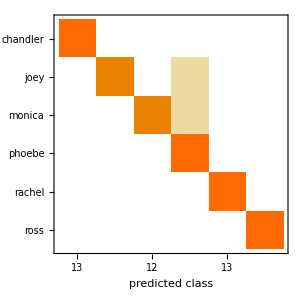

```mathematica
metrics["ConfusionMatrixPlot"]
```

A confusion matrix shows if there are any classes mislabelled as other. From the above confusion matrix we can interpret that there is one image of ‘joey’ mislabelled as ‘chandler’ and vice versa, one image of ‘chandler’ mislabelled as ‘ross’ and one image of ‘monica’ mislabelled as ‘rachel’. Let us have a look at the probability histogram now:

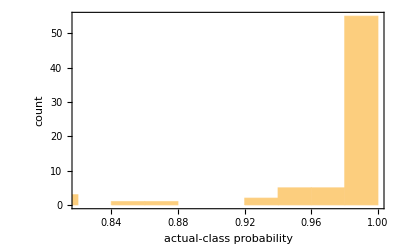

```mathematica
metrics["ProbabilityHistogram"]
```

Majority of predictions lie in the range of probability 0.8-1 which conveys a good fit.
Precision and recall are among the most important metrics to test a models accuracy and interpret it more precisely. Precision, or the positive predictive value, refers to the fraction of relevant instances among the total retrieved instances. Recall, also known as sensitivity, refers to the fraction of relevant instances retrieved over the total amount of relevant instances. Below image will elaborate these concepts more clearly:

```mathematica
-Graphics--Graphics-
```

-Graphics- -Graphics-

```mathematica
metrics["Precision"]
```

<|chandler→1.,joey→1.,monica→1.,phoebe→0.866667,rachel→1.,ross→1.|>

```mathematica
metrics["Recall"]
```

<|chandler→1.,joey→0.923077,monica→0.923077,phoebe→1.,rachel→1.,ross→1.|>

Then we have another metric called as the F1-score which takes into consideration both precision and recall values and can be calculated as (2*precision*recall)/(precision+recall). Below is the F1Score for all the classes of our model.

```mathematica
metrics["F1Score"]
```

<|chandler→1.,joey→0.96,monica→0.96,phoebe→0.928571,rachel→1.,ross→1.|>

Well, we are pretty much done with our model now, why not create a grid interface to try out the model on unknown images?! Will be fun, yeah?

## A Basic Application

We can upload any image from the file system and the model would classify the image as one of the characters from F.R.I.E.N.D.S with the highest possible match (highest probability).

```mathematica
image = Import[StringJoin[dir, "\\unknownimages\\me.jpg"],ImageSize -> 200];
probabilities = Normal[trained[image,"Probabilities"]]
```

{chandler→0.0000223858,joey→0.981002,monica→0.0019521,phoebe→3.69652×10^-13,rachel→0.0170102,ross→0.0000128907}

```mathematica
Evaluate[Framed[Grid[{{Text[Style["Which F.R.I.E.N.D.S. Character Are You?",Bold,24]]},
{Dynamic[image]},{Text[Style[Dynamic[character],{Bold, Italic},18]],
FileNameSetter[Dynamic[file],Appearance->"Select New Image"]},
{Text[Style[Dynamic[prob],14]],Button["Classify Image",image=Import[file];
character = trained[extractFaces[image]];
prob=Normal[trained[image,"Probabilities"]]]}}],FrameStyle->Thick]]
```

Which F.R.I.E.N.D.S. Character Are You? | 
 | 
 | $CellContext`fileOpenAllAutomaticSelect New ImageDialogBoxFileNameSetterAutomatic0Automatic
 | Classify Image

I have pre - imported a file of my image, to import another file click on the ‘Select New Image’ button and hit ‘Classify Image’ to commence the fun! 
I resemble to Phoebe from F.R.I.E.N.D.S, which F.R.I.E.N.D.S character are you?!!

## Future Scope and Applications

The model accuracy can be increased more by maximizing the dataset. More data results in better training and thus better prediction.
Also, the neural net of this model can be reused for a variety of image classification problems, you need not use the ExtractFaces function in a classification problem unless its a human face/image classification problem.

## Bibliography

I have used a variety of resources from the web to get a better understanding of the concepts in the project’s domain and represent the same. 
The web links are listed below:

https://deepai.org/machine-learning-glossary-and-terms/

https://towardsdatascience.com/applied-deep-learning-part-4-convolutional-neural-networks-584bc134c1e2

https://uk.mathworks.com/solutions/deep-learning/convolutional-neural-network.html

https://www.superdatascience.com/blogs/the-ultimate-guide-to-convolutional-neural-networks-cnn